## Решаем уравнение пренебрегая теплопроводностью и с произвольными граничными условиями.

### Параметры

```mathematica
len=1;  (* Размер среды*)
CvI=3/2;CpI=5/2;gI=CpI/CvI;
τ1 =30*60;
τ2 =5*60;
T=10^6.32;
ρ = 10^-12;
kB =1.380649*10^−23; 
Cs0 = √(kB*T/ρ);
v1 = len/τ1 /Cs0;
v2 = len/τ2 /Cs0;
g0=(5 τ2)/(3 τ1);
goi=g0/gI;
amp = 0;
wid =0.05;
pos = 0.5;
Nmax = 30;
```

### Начальные условия

```mathematica
(*начальные условия ro0[z, t=0] = Initial[x_,amp_,wid_,pos_]*)
Initial[x_,amp_,wid_,pos_]:=  amp ⅇ^(-(-pos+x)^2/(2 wid^2))
Initialdt[x_,amp_,wid_,pos_]:= -(amp ⅇ^(-(-pos+x)^2/(2 wid^2)) (-pos+x))/wid^2
Initialdtt[x_,amp_,wid_,pos_]:=1/2 * amp (-(ⅇ^(-(-pos+x)^2/(2 wid^2)))/wid^2+(ⅇ^(-(-pos+x)^2/(2 wid^2)) (-pos+x)^2)/wid^4)
```

### Граничные условия и замена u(x,t) = U(x,t) + v(x,t)

#### Граничные условия, U(x,t) и производные по t

```mathematica
freq=10;
amp2=2;
```

```mathematica
BoundLeft[t_] :=amp2*freq*t*Exp[-freq*t];(*Piecewise[{{Sin[freq*t],t<=Pi/freq},{0,t>Pi/freq}}]*)
(*BoundLeft[t_] := Sin[freq*t]*)
(*BoundRight[t_] := -5*Sin[1*t];*)
BoundRight[t_] := 0;
U[x_,t_] := (BoundRight[t] - BoundLeft[t])/len * x +BoundLeft[t];
```

```mathematica
(*Udt [x_,t_]:=freq Cos[freq t]-freq x Cos[freq t];
Udtt [x_,t_]:= -freq^2 Sin[freq t]+freq^2 x Sin[freq t];
Udttt[x_,t_] :=-freq^3 Cos[freq t]+freq^3 x Cos[freq t];*)
Udt [x_,t_]:=amp2 ⅇ^(-freq t) freq-amp2 ⅇ^(-freq t) freq^2 t-amp2 ⅇ^(-freq t) freq x+amp2 ⅇ^(-freq t) freq^2 t x;
Udtt [x_,t_]:= -2 amp2 ⅇ^(-freq t) freq^2+amp2 ⅇ^(-freq t) freq^3 t+2 amp2 ⅇ^(-freq t) freq^2 x-amp2 ⅇ^(-freq t) freq^3 t x;
Udttt[x_,t_] :=3 amp2 ⅇ^(-freq t) freq^3-amp2 ⅇ^(-freq t) freq^4 t-3 amp2 ⅇ^(-freq t) freq^3 x+amp2 ⅇ^(-freq t) freq^4 t x;
```

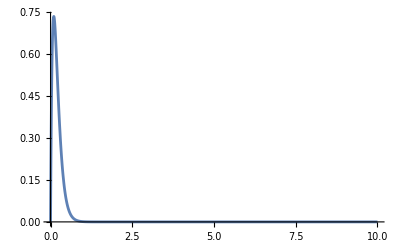

```mathematica
Plot[BoundLeft[t], {t,0,10}, PlotRange->Full ]
```

#### Производные

```mathematica
D[U[x,t], t]
D[D[U[x,t], t],t]
D[D[D[U[x,t], t],t],t]
```

amp2 ⅇ^(-freq t) freq-amp2 ⅇ^(-freq t) freq^2 t-amp2 ⅇ^(-freq t) freq x+amp2 ⅇ^(-freq t) freq^2 t x

-2 amp2 ⅇ^(-freq t) freq^2+amp2 ⅇ^(-freq t) freq^3 t+2 amp2 ⅇ^(-freq t) freq^2 x-amp2 ⅇ^(-freq t) freq^3 t x

3 amp2 ⅇ^(-freq t) freq^3-amp2 ⅇ^(-freq t) freq^4 t-3 amp2 ⅇ^(-freq t) freq^3 x+amp2 ⅇ^(-freq t) freq^4 t x

#### Раскладываем неоднородность в ряд дяди Фурье

```mathematica
UI3ro[amp_,wid_,pos_, len_,n_,t_] =((n π-Sin[n π]) (4000 Cos[2 t]+Sin[2 t]))/(250 n^2 π^2)
```

```mathematica
(2/len)*Integrate[(-Udttt[z, t]-v2 * Udtt[z,t])*Sin[Pi*n*z/len], {z, 0, len}]
```

((n π-Sin[n π]) (4000 Cos[2 t]+Sin[2 t]))/(250 n^2 π^2)

### Интегралы для определения констант

#### Интегралы для задачи Неймана (производные на границе равны 0)

```mathematica
I10Hro[amp_,wid_,pos_, len_]:=(1/len)*Integrate[Initial[z,amp,wid,pos] , {z, 0, len} ];
I20Hro[amp_,wid_,pos_, len_]:=(1/len)*Integrate[Initialdt[z,amp,wid,pos], {z, 0, len}];
I30Hro[amp_,wid_,pos_, len_]:=(1/len)*Integrate[Initialdtt[z,amp,wid,pos], {z, 0, len}];
```

```mathematica
I1Hro[amp_,wid_,pos_, len_,n_]=(2/len)*Integrate[(Initial[z,amp,wid,pos])*Cos[Pi*n*z/len], {z, 0, len}];
I2Hro[amp_,wid_,pos_, len_,n_]=(2/len)*Integrate[(Initialdt[z,amp,wid,pos])*Cos[Pi*n*z/len], {z, 0, len}];
I3Hro[amp_,wid_,pos_, len_,n_]=(2/len)*Integrate[(Initialdtt[z,amp,wid,pos])*Cos[Pi*n*z/len], {z, 0, len}];
```

#### Интегралы для задачи Дирихле

```mathematica
I1InHro[amp_,wid_,pos_, len_,n_]=(2/len)*Integrate[(Initial[z,amp,wid,pos]- U[z,0])*Sin[Pi*n*z/len], {z, 0, len}];
I2InHro[amp_,wid_,pos_, len_,n_]=(2/len)*Integrate[(Initialdt[z,amp,wid,pos]- Udt[z,0])*Sin[Pi*n*z/len], {z, 0, len}];
I3InHro[amp_,wid_,pos_, len_,n_]=(2/len)*Integrate[(Initialdtt[z,amp,wid,pos]- Udtt[z,0])*Sin[Pi*n*z/len], {z, 0, len}];
```

```mathematica
UI3ro[amp_,wid_,pos_, len_,n_,t_] =(2/len)*Integrate[(-Udttt[z, t]-v2 * Udtt[z,t])*Sin[Pi*n*z/len], {z, 0, len}];
```

### Решение кубического характеристического уравнения

#### Формулы Кардано

```mathematica
(*Задаем собсвенные числа, на основе решения уравнения для координаты*)
λ[n_]:=((Pi*n)/len)^2   ;
(*Задаем величину D1, которая напрямую связана с дискриминантом кубического уравнения по времени и опредлеяет какие корни по типу*)
P[n_]:=(3λ[n]*gI-v2^2)/9;                      
Q[n_]:=(2 v2^3-9v2*λ[n]*gI+27v2*λ[n]*g0)/54;
D1[n_]:=P[n]^3+Q[n]^2;
(*Ругает меня вольфрама, что скармливаю ей комплексную дичь*) 
A[n_]:=If[D1[n]>0,
CubeRoot[-Q[n]+√D1[n]],
N[(-Q[n]+√D1[n])^(1/3)]];
(*A[n_]:=N[(-Q[n]+√D1[n])^(1/3)]*)
B[n_]:=-P[n]/A[n];
```

#### Итого

```mathematica
wEI[n_]:=-v2/3+A[n]+B[n];  
wAI[n_]:=-(v2/3+(A[n]+B[n])/2); 
wAR[n_]:=(A[n]-B[n])/2 √3; 
w1[n_]:=If[D1[n]<0,I*Im[I*(-v2/3+A[n]+B[n])],I*(-v2/3+A[n]+B[n])];w2[n_]:=If[D1[n]<0,I*Im[(A[n]-B[n])/2 √3- I*(v2/3+(A[n]+B[n])/2)],(A[n]-B[n])/2 √3- I*(v2/3+(A[n]+B[n])/2)];w3[n_]:=If[D1[n]<0,I*Im[-(A[n]-B[n])/2- I*(v2/3+(A[n]+B[n])/2)],-(A[n]-B[n])/2- I*(v2/3+(A[n]+B[n])/2)];
```

### Находим константы С

#### Для задачи Неймана (производные на границе равны 0)

```mathematica
I10ro[amp_,wid_,pos_, len_] =I10Hro[amp,wid,pos, len];
I20ro[amp_,wid_,pos_, len_]=I20Hro[amp,wid,pos, len];
I30ro[amp_,wid_,pos_, len_]=I30Hro[amp,wid,pos, len];
I1ro[amp_,wid_,pos_, len_,n_]=I1Hro[amp,wid,pos, len,n];
I2ro[amp_,wid_,pos_, len_,n_]=I2Hro[amp,wid,pos, len,n];
I3ro[amp_,wid_,pos_, len_,n_]=I3Hro[amp,wid,pos, len,n];
```

#### Для задачи Дирихле

```mathematica
I1ro[amp_,wid_,pos_, len_,n_]=I1InHro[amp,wid,pos, len,n];
I2ro[amp_,wid_,pos_, len_,n_]=I2InHro[amp,wid,pos, len,n];
I3ro[amp_,wid_,pos_, len_,n_]=I3InHro[amp,wid,pos, len,n];
```

#### Сами константы C

```mathematica
(*константы для ro0[x,t]*)
C10ro:= 1/v2^2 * I30ro[amp,wid,pos,len];
C20ro:=I20ro[amp,wid,pos, len]+ v2*C10ro ;
C30ro:= I10ro[amp,wid,pos, len] - C10ro;
```

```mathematica
C2nro[n_]:=Re[(I3ro[amp,wid,pos, len,n]+2*wAI[n]*I2ro[amp,wid,pos, len,n]-2*wAI[n]*wEI[n]*I1ro[amp,wid,pos, len,n]-wEI[n]^2*I1ro[amp,wid,pos, len,n])/(-wAI[n]^2-wAR[n]^2-wEI[n]^2-2*wAI[n]*wEI[n])];
C1nro[n_]:=Re[I1ro[amp,wid,pos, len,n] - C2nro[n]];
C3nro[n_]:= Re[(I2ro[amp,wid,pos, len,n]-wEI[n] *I1ro[amp,wid,pos, len,n] +(wAI[n]+wEI[n] )* C2nro[n])/wAR[n]];
```

```mathematica
C0ro[n_]:=Sign[C2nro[n]]*(√(C2nro[n]^2+C3nro[n]^2))/2;
phi[n_]:=ArcTan[C3nro[n]/C2nro[n]];
```

```mathematica
C3pro[n_] :=((I1ro[amp,wid,pos, len,n]*w1[n]-I2ro[amp,wid,pos, len,n])w2[n]-I2ro[amp,wid,pos, len,n]w1[n]+I3ro[amp,wid,pos, len,n])/(w3[n]^2-(w2[n]+w1[n])w3[n]+w1[n]w2[n]);
C2pro[n_]:=(I2ro[amp,wid,pos, len,n]-w1[n]*I1ro[amp,wid,pos, len,n]-(w3[n]-w1[n])*C3pro[n])/(w2[n]-w1[n]);
C1pro[n_] := I1ro[amp,wid,pos, len,n]-C2pro[n]-C3pro[n];
```

### Находим константы D для неоднородного уравнения Дирихле

```mathematica
D2nro[n_, s_]=(UI3ro[amp,wid,pos, len,n,s])/(-wAI[n]^2-wAR[n]^2-wEI[n]^2-2*wAI[n]*wEI[n]);
D1nro[n_, s_]=- D2nro[n,s];
D3nro[n_,s_]=((wAI[n]+wEI[n] )* D2nro[n,s])/wAR[n];
```

```mathematica
D0ro[n_,s_]:=Sign[D2nro[n,s]]*(√(D2nro[n,s]^2+D3nro[n,s]^2))/2;
Dphi[n_,s_]:=ArcTan[D3nro[n,s]/D2nro[n,s]];
```

```mathematica
D3pro[n_,s_] = Re[UI3ro[amp,wid,pos, len,n,s]/(w3[n]^2-(w2[n]+w1[n])w3[n]+w1[n]w2[n])];
D2pro[n_,s_]=Re[(-(w3[n]-w1[n])*D3pro[n,s])/(w2[n]-w1[n])];
D1pro[n_,s_] = Re[-D2pro[n,s]-D3pro[n,s]];
```

### Итоговое решение

#### Для задачи Неймана (производные на границе равны 0)

```mathematica
ro01[t_] =C10ro  * Exp[-v2*t]+C20ro*t +C30ro;
ro1[z_,t_, n_] = If[D1[n]>0,
C1nro[n]*Exp[wEI[n]*t]*Cos[Pi*n/len*z]+C0ro[n]*Exp[wAI[n]*t]*(Cos[wAR[n]*t+Pi*n/len*z-phi[n]]+Cos[wAR[n]*t-Pi*n/len*z-phi[n]]),
(C1pro[n]*Exp[w1[n]*t]+C2pro[n]*Exp[w2[n]*t]+C3pro[n]*Exp[w3[n]*t])*Cos[Pi*n/len*z]] ;

ro[z_,t_]= Re[ro01[t]+Sum[ro1[z,t,n],{n,Nmax}]];
```

#### Для задачи Дирихле

```mathematica
ro1[z_,t_, n_] = If[D1[n]>0,
C1nro[n]*Exp[wEI[n]*t]*Sin[Pi*n/len*z]+Exp[wAI[n]*t]*(C2nro[n]*Cos[wAR[n]*t]+C3nro[n]*Sin[wAR[n]*t])*Sin[Pi*n/len *z],
(C1pro[n]*Exp[w1[n]*t]+C2pro[n]*Exp[w2[n]*t]+C3pro[n]*Exp[w3[n]*t])*Sin[Pi*n/len*z]] ;

roHomogeneous[z,t]=Sum[ro1[z,t,n],{n,Nmax}];
```

```mathematica
ro2[z_,t_,s_, n_] = If[D1[n]>0,
D1nro[n,s]*Exp[wEI[n]*t]*Sin[Pi*n/len*z]+Exp[wAI[n]*t]*(D2nro[n,s]*Cos[wAR[n]*t]+D3nro[n,s]*Sin[wAR[n]*t])*Sin[Pi*n/len *z],
(D1pro[n,s]*Exp[w1[n]*t]+D2pro[n,s]*Exp[w2[n]*t]+D3pro[n,s]*Exp[w3[n]*t])*Sin[Pi*n/len*z]] ;
```

```mathematica
roInHomogeneous[z_,t_] = Sum[Integrate[N[ro2[z,t,s,n]],{s,0,t}],{n,Nmax} ]; //AbsoluteTiming
```

{190.05,Null}

```mathematica
ro[z_,t_] = N[Re[roInHomogeneous[z,t]+roHomogeneous[z,t]+U[z,t]]];
```

```mathematica
nt = 1
Simplify[D[D[D[roInHomogeneous[z,t, nt],t],t],t]+v2*(D[D[roInHomogeneous[z,t],t],t]-g0*D[D[roInHomogeneous[z,t],z],z])-5/3 * D[D[D[ro[z,t],z],z],t]]
```

1

$Aborted

```mathematica
roBefore[z_,t_]=ro[z_,t_]
```

### Творим красоту

General::munfl: 1/2.71828^3326.36 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^3826.36 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

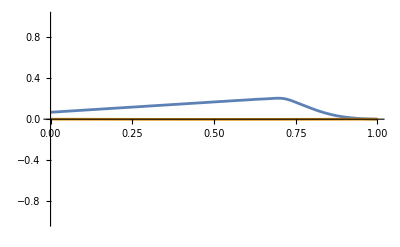

```mathematica
Plot[{ro[x,1], ro[x,100]},{x, 0, len}, PlotRange->{{0,len},{-1,1}}]
```

```mathematica
PlotList=Table[Plot[{ro[x,t]},{x, 0, len},PlotRange->{{0,len},{-10,10}}],{t,0,2,0.1}];//AbsoluteTiming
```

{242.425,Null}

```mathematica
ListAnimate[PlotList]
```

```mathematica
Export["region3_1000_1.avi",PlotList]
```

region3_1000_1.avi

#### Time-distance plot

```mathematica
DensityPlot[ro[z,t], {z,0,len}, {t, 0,10},PlotPoints->{10,100}]
```

-Graphics-

### Декремент затухания

```mathematica
zfixed=len/2;
```

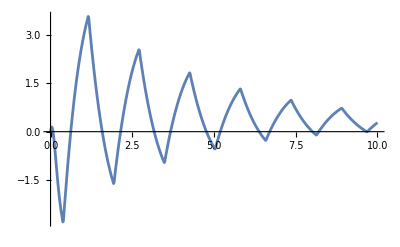

```mathematica
Plot[{ro[zfixed,t]}, {t,0,10}, PlotRange->All]
```

```mathematica
tmin = 20;
tmax = 30;
step = (tmax-tmin)/100;
data = Table[{t,ro[zfixed,t]}, {t, Range[tmin,tmax,step]}];
```

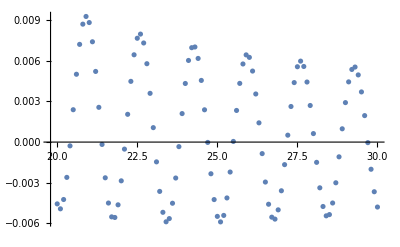

```mathematica
ListPlot[{data}]
```

FittedModel[-81.4229 ⅇ^(-0.258429 t) Sin[50.6054+4.04091 t]]

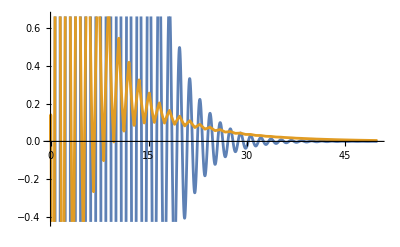

```mathematica
nlm=NonlinearModelFit[data, {a*Exp[wAI[1]*t]*Sin[wAR[1]*t+ph]}, {a,ph}, t]
Plot[{nlm[t], ro[zfixed, t]}, {t,0,50}]
```

```mathematica
Table[{n, wAI[n], wAR[n], wEI[n]}, {n, Range[1, 10]}]
```

```mathematica
Table[{n, C1nro[n], C2nro[n], C3nro[n]}, {n, Range[1, 10]}]
```

{{1,15.8704,-15.8704,-1.72833},{2,1.9848,-1.9848,-0.696872},{3,0.588144,-0.588144,-0.331447},{4,0.248131,-0.248131,-0.190714},{5,0.127045,-0.127045,-0.123323},{6,0.0735221,-0.0735221,-0.0861183},{7,0.0462999,-0.0462999,-0.0634821},{8,0.0310174,-0.0310174,-0.0487086},{9,0.0217845,-0.0217845,-0.0385427},{10,0.015881,-0.015881,-0.0312526}}

```mathematica
Table[{n,C1pro[n], C2pro[n], C3pro[n]}, {n, Range[1, 10]}]
```

{{1,-29.2013+1.51233 ⅈ,8.72754+0.154963 ⅈ,20.4738-1.6673 ⅈ},{2,-3.92841+0.141743 ⅈ,0.941598-0.00423783 ⅈ,2.98681-0.137505 ⅈ},{3,-1.24865+0.0373466 ⅈ,0.236111-0.00357462 ⅈ,1.01254-0.033772 ⅈ},{4,-0.562626+0.0147757 ⅈ,0.0816058-0.00199677 ⅈ,0.48102-0.0127789 ⅈ},{5,-0.306438+0.00726429 ⅈ,0.0325775-0.00117245 ⅈ,0.27386-0.00609184 ⅈ},{6,-0.187973+0.00408784 ⅈ,0.013529-0.000736411 ⅈ,0.174444-0.00335143 ⅈ},{7,-0.125073+0.00252209 ⅈ,0.00516815-0.000489794 ⅈ,0.119905-0.00203229 ⅈ},{8,-0.0882772+0.00166339 ⅈ,0.00121729-0.000341211 ⅈ,0.0870599-0.00132218 ⅈ},{9,-0.0651522+0.00115393 ⅈ,-0.000721628-0.000246793 ⅈ,0.0658738-0.000907139 ⅈ},{10,-0.0497941+0.000832868 ⅈ,-0.00167532-0.000184082 ⅈ,0.0514694-0.000648785 ⅈ}}

```mathematica
table = Table[FindMaximum[ro[zfixed, t],{t,t0}], {t0, Range[tmin, tmax, 1.8]}]
```

{{0.0198861,{t→15.8512}},{0.00799773,{t→22.5818}},{0.00711963,{t→24.2558}},{0.00648092,{t→25.9287}},{0.00598408,{t→27.6011}},{0.00557395,{t→29.2732}}}

```mathematica
Table[Log[table[[n]][[1]]/table[[n+1]][[1]]]/(table[[n]][[2]][[1]][[2]]-table[[n+1]][[2]][[1]][[2]]), {n, Range[Length[table]-1]}]
```

{-0.0488155,-8.03678×10^-6,-0.00465471,7.67954×10^-8,-0.00465471,-0.00465471,-0.0789816,-0.0261323,-0.052366}

```mathematica
Mean[{-0.04881545802483862,-0.004654705929257516,-0.004654705921180983,-0.0046547059211915764,-0.07898159292860794,-0.026132323423949097,-0.05236597654949698}]
```

-0.0314656

```mathematica
rogreen[z,t]
```

rogreen[z,t]

```mathematica
Plot[rored[zfixed,t],{t,0,1}]
```

-Graphics-